```mathematica
Clear["Global`*"];
(*Ініціалізвція змінних*)
p=1; q=4;Δ=0.1;
F1t[x1_,x2_]:=(x1-p)^2+(x2-q)^2-(2x1 x2)/(p+q); F1[X_]:=F1t[X⟦1⟧,X⟦2⟧];
F2t[x1_,x2_]:=(1.5−x1+x1 x2)^2+(2.25−x1+x1 x2^2)^2 +(2.625−x1+x1 x2^3)^2;F2[X_]:=F2t[X⟦1⟧,X⟦2⟧];
```

```mathematica
(*Розрахунок градієнту*)
F1Gradt[x1_,x2_]:={(F1t[x1+Δ,x2]-F1t[x1-Δ,x2])/(2Δ),(F1t[x1,x2+Δ]-F1t[x1,x2-Δ])/(2Δ)};F1Grad[X_]:=F1Gradt[X⟦1⟧,X⟦2⟧];
F2Gradt [x1_,x2_]:= {(F2t[x1+Δ,x2]-F2t[x1-Δ,x2])/(2Δ),(F2t[x1,x2+Δ]-F2t[x1,x2-Δ])/(2Δ)};F2Grad[X_]:=F2Gradt[X⟦1⟧,X⟦2⟧];
```

{2.01318×10^15,1.84081×10^15}

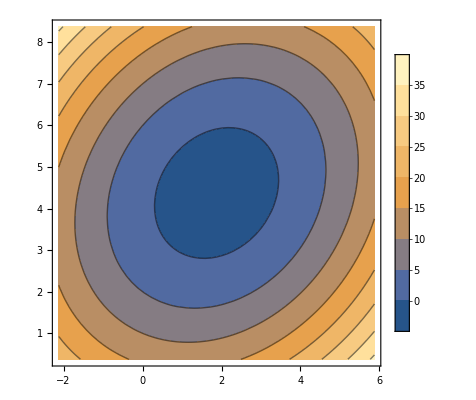

```mathematica
(*Квадратична функція*)
start = {1.0,1.0};
α=1;
X[0]= start;
For[i=1,i<1000,i++,
X[i]=X[i-1]-α F1Grad[X[i-1]];
]
Print[X[999]]
(*Побудова графіку*)
сp =ContourPlot[F1t[x1,x2],{x1,-4 + 15/8,4 + 15/8},{x2,-4+35/8,4+35/8},PlotLegends->Automatic];
lp = ListLinePlot[Table[X[i],{i,0,999}],PlotRange->All,PlotStyle->Red];

Show[{сp, lp}]
```

{3.19734,0.537059}

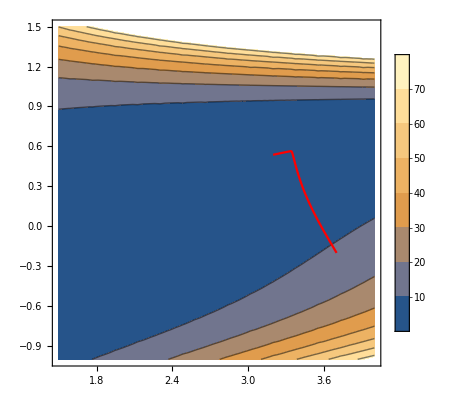

```mathematica
(*Індивідуальна функція*)
start = {3.7,-0.2};
α = 0.001;
Y[0]= start;
For[i=1,i<1000,i++,
Y[i]=Y[i-1]-α F2Grad[Y[i-1]];
]
Print[Y[999]]
(*Побудова графіку*)
сp =ContourPlot[F2t[x1,x2],{x1,1.5,4},{x2,-1,1.5},PlotLegends->Automatic];
lp = ListLinePlot[Table[Y[i],{i,0,999}],PlotRange->All,PlotStyle->Red];

Show[{сp, lp}]
```